# Num Analy HW 4

## 3.1

```mathematica
(*
From http://stackoverflow.com/questions/8410613/list-manipulation-in-mathematica-pertaining-to-lagrange-interpolation-polynomial
*)
LagrangePoly[pts_?MatrixQ,var_: x]/;MatchQ[Dimensions[pts],{_,2}]:=With[{k=Length[pts]},Sum[pts[[j,2]] Product[If[j≠m,(var-pts[[m,1]])/(pts[[j,1]]-pts[[m,1]]),1],{m,1,k}],{j,1,k}]]

NewtonPoly[XY_]:=
Module[{d,j,i,n,X,Y},
X = Transpose[XY]_⟦1⟧; 
Y = Transpose[XY]_⟦2⟧; 
n = Length[XY]-1; 
d = Table["",{n+1},{n+1} ]; 
d_⟦All,1⟧ = Y_⟦All⟧; 
For[ j=1, j≤n, j++,
For[ i=j, i≤n, i++,
d_⟦i+1,j+1⟧ = (d_⟦i+1,j⟧ - d_⟦i,j⟧)/(X_⟦i+1⟧ - X_⟦i+1-j⟧) ]; ]; 
For[ i=0, i≤n, i++,
p[i+1,x_] = ∏_(j=1)^i (x-X_⟦j⟧) ]; 
Dtable=d;
Return[  ∑_(i=0)^n d_⟦i+1,i+1⟧ p[i+1,x] ]; ]
```

### 7

```mathematica
Print["P(0) = ",((x-1)(x-2)(x-3)(x-4)(x-5)(x-6)(x-7)(x-8)(x-9)(x-10)-39916756)/.x->0]
```

P(0) = -36287956

### 9

(a)

```mathematica
LagrangePoly[{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,10}},x]//Expand
```

10-(49 x)/2+(203 x^2)/9-(245 x^3)/24+(175 x^4)/72-(7 x^5)/24+x^6/72

(b)

```mathematica
Expand[LagrangePoly[{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,10},{8,70.}},x]]
```

10.-24.5 x+22.5556 x^2-10.2083 x^3+2.43056 x^4-0.291667 x^5+0.0138889 x^6

### 13

```mathematica
p=LagrangePoly[{{1800,280},{1850,283},{1900,291},{2000,370}},x];Print["(a) in 1950: ",p/.x->1950]
Print["(a) in 2050: ",p/.x->2050]
```

(a) in 1950: 316

(a) in 2050: 465

## 3.2 Text

### 5

I expect it to be smaller for .35 since it is more in the center of the points.

```mathematica
f[x_]=x^5;
pp=LagrangePoly[Table[{k,f[k]},{k,{.1,.2,.3,.4,.5,.6}}],x];
Print[".35 residual is ",Total[Abs[Map[f,{.1,.2,.3,.4,.5,.6}]-pp/.x->.35]]]
Print[".55 residual is ",Total[Abs[Map[f,{.1,.2,.3,.4,.5,.6}]-pp/.x->.55]]]
```

.35 residual is 0.11649

.55 residual is 0.234824

## 3.2 Computer

### 1

```mathematica
P[x_]=NewtonPoly[{{.6,1.433329},{.7,1.632316},{.8,1.896481},{.9,2.247908},{1.0,2.718282}}];
P[x]//Expand
Print["(b)\n"]
Print["P(0.82): ",P[0.82]," and P(0.98): ",P[0.92]]
```

1.58117-3.47361 x+8.9309 x^2-8.32058 x^3+4.00042 x^4

"(b)

```mathematica
Print["Error Bound: for .82 and .98 respectively ",Table[(((x-.6)(x-.7)(x-.8)(x-.9)(x-1.0)/ 5!) *D[E^(x^2),{x,5}])/.x->y,{y,{.82,.98}}]]
Print["Actual Error: for .82 and .98 respectively ",Table[Abs[E^(x^2)-P[x]],{x,{.82,.98}}]]
```

Error Bound: for .82 and .98 respectively {0.0000246353,-0.000198233}

Actual Error: for .82 and .98 respectively {0.0000233485,0.000106605}

Error Plot on [.5,1]

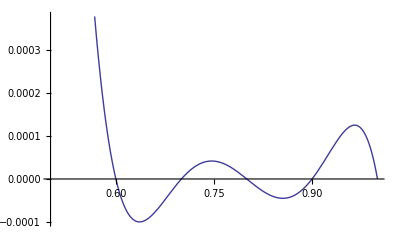

Error Plot on [0,2]

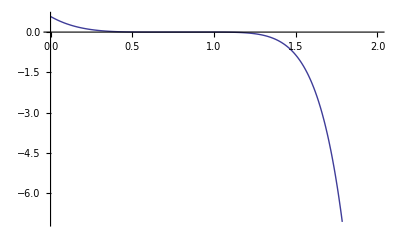

```mathematica
Print["Error Plot on [.5,1]"]
Plot[P[x]-E^(x^2),{x,.5,1}]
Print["Error Plot on [0,2]"]
Plot[P[x]-E^(x^2),{x,0,2}]
```

### 3

3.73796×10^26-1.6834×10^24 x+3.36945×10^21 x^2-3.93412×10^18 x^3+2.95291×10^15 x^4-1.47761×10^12 x^5+4.92924×10^8 x^6-105710. x^7+13.2241 x^8-0.000735246 x^9

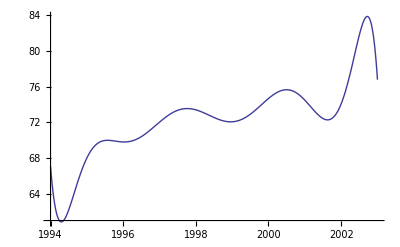

68.008

In 2010 this predicts it will be -1.95165×10^6

Yes the Runge Phenomena is strongly present - this is not a good model

In 2010 this predicts it will be -1.95165×10^6

```mathematica
Po=LagrangePoly[{
{1994,67.052},{1995,68.008},{1996,69.803},{1997,72.024},{1998,73.400},{1999,72.063},{2000,74.669},{2001,74.487},{2002,74.065},{2003,76.777}
},x];
Po//Expand
Plot[Po/.x->y,{y,1994,2003}]
Po/.x->1995
Print["In 2010 this predicts it will be ",Po/.x->2010]
Print["Yes the Runge Phenomena is strongly present - this is not a good model"]
```